# 1D Graph states generation on Rydberg neutral atoms

Source of the experiment : www.nature.com/articles/s41586-022-04592-6

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"36"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink and use pre-compiled link suitable for gpu acceleration

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_gpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../../../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz
Length unit: μm

Accepts 2 or 3 dimensional coordinate format

```mathematica
Options[RydbergHub]={
QubitNum-> 12,
AtomLocations->Association@Table[j->{j,0},{j,0,11}],
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.001, 01->0.03|>,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.001,
DurInit->5*10^5,
DurMove->100,
HeatFactor->10,
FidMeas-> 0.975,
DurMeas-> 10,
ProbLossMeas-> 0.0001,
ProbLeakCZ-><|01->0.01,11->0.0001|>
};
```

## Preparation

### Plots on the paper

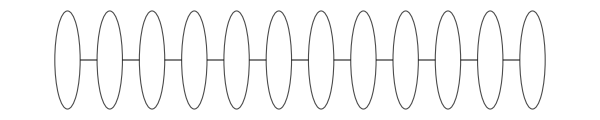

~/vqd/img/graph1d.pdf

```mathematica
g=Graph[#<->#+1&/@Range[0,10]];
Graph[g,VertexSize->0.6,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{13,FontFamily->"Serif"},ImageSize->600,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center]]
Export["~/vqd/img/graph1d.pdf",%]
```

```mathematica
showgs[title_:"",opt_:{}]:=PlotAtoms[devGS,Sequence@@opt,ImageSize->900,ShowBlockade->Range[0,11],LabelStyle->Directive[17,Black],BaseStyle->{16,FontFamily->"Times"},PlotRange->{{-1,37},{-1.3,1.3}},Epilog->Inset[Style[title,{Purple,Italic}],Scaled[{0.96,0.15}]],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],
FrameTicks->{{{-1,0,1},None},{Automatic,None}}
];
```

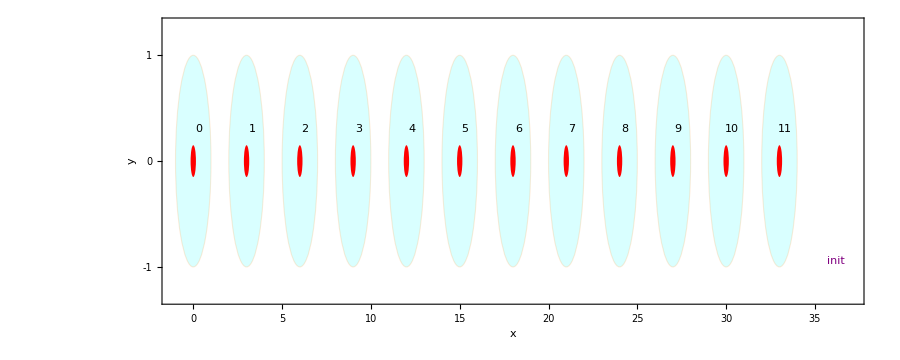

```mathematica
devGS=RydbergHub[];
showgs["init"]
```

```mathematica
circ1=CircRydbergHub[Flatten@{{Subscript[Init, #],Subscript[Ry, #][π/2]}&/@Range[0,11]},RydbergHub[],Parallel->True];
circ2={{Subscript[ShiftLoc, Sequence@@Range[1,11,2]][{-0.75,0}]}};
circ3={Subscript[C, #][Subscript[Z, #+1]]&/@Range[0,10,2]};
circ4={{Subscript[ShiftLoc, Sequence@@Range[1,11,2]][{1.5,0}]}};
circ5={Subscript[C, #][Subscript[Z, #+1]]&/@Range[1,9,2]};
```

```mathematica
devGS=RydbergHub[];
f1=showgs["initial",{ImagePadding->{{30,20},{0,0}}}];
noisycirc1=InsertCircuitNoise[circ1,devGS];
noisycirc2=InsertCircuitNoise[circ2,devGS];
f2=showgs["move 1",{ImagePadding->{{30,20},{0,0}}}];
noisycirc3=InsertCircuitNoise[circ3,devGS];
noisycirc4=InsertCircuitNoise[circ4,devGS];
f3=showgs["move 2",{ImagePadding->{{30,20},{20,0}}}];
noisycirc5=InsertCircuitNoise[circ5,devGS];
```

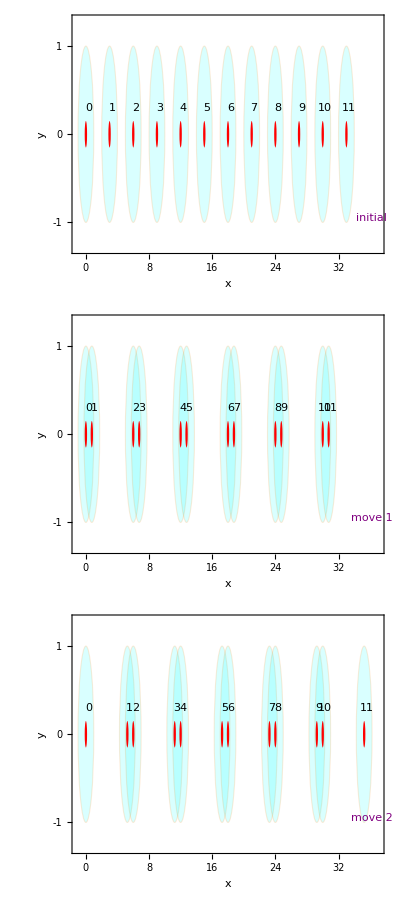

~/vqd/img/rydberg_graph.pdf

```mathematica
Column[{f1,f2,f3},Spacings->0]
Export["~/vqd/img/rydberg_graph.pdf",%]
```

#### Initialisation test

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[12];
ρinit=CreateDensityQureg[12];
ρwork=CreateDensityQureg[12];
```

```mathematica
(*returns graph state stabilizer of a node*)
stabgs[graph_,node_]:=With[{neig=Complement[VertexList@NeighborhoodGraph[graph,node],{node}]},
ToExpression[StringRiffle[Join[{Subscript[X, node]},Subscript[Z, #]&/@neig]]]]
```

Total  circuit excluding measurement

```mathematica
SetQuregMatrix[ρinit,RandomMixState[12]];
```

```mathematica
totalcirc=Join@@(ToExpression["circ"<>ToString@#]&/@Range[1,5])
```

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8,Init_9,Init_10,Init_11},{Ry_0[π/2],Ry_1[π/2],Ry_2[π/2],Ry_3[π/2],Ry_4[π/2],Ry_5[π/2],Ry_6[π/2],Ry_7[π/2],Ry_8[π/2],Ry_9[π/2],Ry_10[π/2],Ry_11[π/2]},{ShiftLoc_(1,3,5,7,9,11)[{-0.75,0}]},{C_0[Z_1],C_2[Z_3],C_4[Z_5],C_6[Z_7],C_8[Z_9],C_10[Z_11]},{ShiftLoc_(1,3,5,7,9,11)[{1.5,0}]},{C_1[Z_2],C_3[Z_4],C_5[Z_6],C_7[Z_8],C_9[Z_10]}}

```mathematica
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[]];
(*Simplify, remove errors with zero-parameters *)
enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
```

Run the circuit without measurement. We start from an unknown mixed state

```mathematica
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc]
```

{}

Benchmarking the perfect measurement. Quoted value: 0.91. Noisy: 0.87

{0.966834,0.965942,0.966847,0.965945,0.966847,0.965945,0.966847,0.965945,0.966847,0.965945,0.966844,0.965932}

0.966393

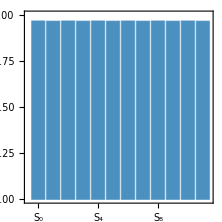

```mathematica
stabdata=CalcExpecPauliString[ρ,stabgs[g,#],ρwork]&/@Range[0,11]
Mean@stabdata
BarChart[stabdata,ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,11]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1,ChartStyle->ColorData["Rainbow"][0.3],PlotRange->{Automatic,{0,1}}]
```

Gather the statistics by shots

Note that the “X” measurement done in the circuit is flipped: H=Ry[π/2]X

```mathematica
CalcCircuitMatrix[{Subscript[Ry, 0][π/2],Subscript[X, 0]}]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
DrawCircuit@{Subscript[Ry, 0][π/2],Subscript[X, 0]}
```

-Graphics-

```mathematica
CalcCircuitMatrix[Subscript[X, 0]].CalcCircuitMatrix[Subscript[Ry, 0][π/2]]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
(*Two measurement settings: {Subscript[S, j]} where (1) j are even, (2) j are odd  
Put measurements at the very last!*)
evensm={Subscript[Ry, #][π/2]&/@Range[0,11,2],Subscript[M, #]&/@Range[0,11]};
oddsm={Subscript[Ry, #][π/2]&/@Range[1,11,2],Subscript[M, #]&/@Range[0,11]};
```

```mathematica
SimulateGraphState[ρ_,ρinit_,ρwork_,ρstore_,nshots_,options_:{}]:=Module[{noisycirc,enoisycirc,emeasnoisy,omeasnoisy,statevenmeas={},statoddmeas={},scount,outeig,stabideal,totalcirc},
totalcirc={{Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8],Subscript[Init, 9],Subscript[Init, 10],Subscript[Init, 11]},{Subscript[Ry, 0][π/2],Subscript[Ry, 1][π/2],Subscript[Ry, 2][π/2],Subscript[Ry, 3][π/2],Subscript[Ry, 4][π/2],Subscript[Ry, 5][π/2],Subscript[Ry, 6][π/2],Subscript[Ry, 7][π/2],Subscript[Ry, 8][π/2],Subscript[Ry, 9][π/2],Subscript[Ry, 10][π/2],Subscript[Ry, 11][π/2]},{Subscript[ShiftLoc, 1,3,5,7,9,11][{-0.75,0}]},{Subscript[C, 0][Subscript[Z, 1]],Subscript[C, 2][Subscript[Z, 3]],Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 6][Subscript[Z, 7]],Subscript[C, 8][Subscript[Z, 9]],Subscript[C, 10][Subscript[Z, 11]]},{Subscript[ShiftLoc, 1,3,5,7,9,11][{1.5,0}]},{Subscript[C, 1][Subscript[Z, 2]],Subscript[C, 3][Subscript[Z, 4]],Subscript[C, 5][Subscript[Z, 6]],Subscript[C, 7][Subscript[Z, 8]],Subscript[C, 9][Subscript[Z, 10]]}};
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[Sequence@@options]];
(*Simplify, remove errors with zero-parameters *)
     enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc];
CloneQureg[ρstore,ρ];
emeasnoisy=ExtractCircuit@InsertCircuitNoise[evensm,RydbergHub[Sequence@@options]];
omeasnoisy=ExtractCircuit@InsertCircuitNoise[oddsm,RydbergHub[Sequence@@options]];

Table[
(* Note that this is okay because we don't have any function that depends on the absolute time.*)
(* even measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statevenmeas,Flatten@ApplyCircuit[ρ,emeasnoisy]];
(* odd measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statoddmeas,Flatten@ApplyCircuit[ρ,omeasnoisy]];
,{nshots}];
(* stabilizer count *)
scount=Association@Table[j->0,{j,VertexList@g}];
(* First measurement setting: X,Z,X,Z...*)
Table[
outeig=Table[
If[EvenQ[k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
(* +1 - -1 *)
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[g,node]]);
,{node,0,11,2}];
,{out,statevenmeas}];

(* Second measurement setting: Z,X,Z,X...*)
Table[
outeig=Table[
If[OddQ[k-1],
out[[k]]/.{0:>-1}, (*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[g,node]]);
,{node,1,11,2}];
,{out,statoddmeas}];
stabideal=CalcExpecPauliString[CloneQureg[ρ,ρstore],stabgs[g,#],ρwork]&/@Range[0,11];
<|"opt"->RydbergHub[Sequence@@options][OptionsUsed],"outeven"->statevenmeas,"outodd"->statoddmeas,"scount"->scount,"sideal"->stabideal|>
]

drawChart[res_,expresults_]:=With[{scount=res["scount"],nshots=res["outeven"]//Length,stabideal=res["sideal"]},
Show[
BarChart[Values@scount/nshots,
ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,11]),
Frame->True,FrameStyle->Directive[Black,Thick],
AspectRatio->1.2,
ChartStyle->ColorData["DeepSeaColors"][0.7],
PlotRange->{Automatic,{-0.05,1}}]
,
BarChart[expresults,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]]
,
ListPlot[stabideal,Joined->True,PlotMarkers->{"■",15},PlotStyle->RGBColor[0.6913629326773305, 0.22460288235842985, 0.347286180798712]]
,
ImageSize->{Automatic,250},Background->White,LabelStyle->{10,FontFamily->"Serif"},ImagePadding->{{30,5},{30,10}}
]
]

showResults[res_,expresults_]:=With[
{dev=RydbergHub[Sequence@@res[["opt"]]],nshots=res["outeven"]//Length}
,
<|"nshots"->ToString@nshots,
"chart"->drawChart[res,expresults],
"benchmark"->Table[Between[res[["scount"]][j-1]/nshots,Sort[expresults[[j]][[1]]+{1,-1}*expresults[[j]][[2]]]],{j,Length@expresults}],
"erravg"->Mean@Abs[N[Values@res[["scount"]]/nshots]-expresults],
"errmax"->Max@Abs[N[Values@res[["scount"]]/nshots]-expresults],
"stabavg"->N@Mean@Values@res[["scount"]]/nshots,
"nospamavg"->Mean@res[["sideal"]]|>
]
```

## Simulating the stabiliser measurement

### Quoted from the paper

```mathematica
cs1dmean={0.8814814814814814,0.8314814814814814,0.8888888888888887,0.8629629629629629,0.8814814814814814,0.8796296296296295,0.8555555555555554,0.8759259259259258,0.8722222222222221,0.8777777777777775,0.8462962962962962,0.8925925925925925}
cs1dminus={0.8537037037037036,0.8018518518518518,0.8629629629629629,0.8333333333333333,0.8537037037037036,0.8537037037037036,0.8277777777777777,0.8481481481481481,0.8444444444444444,0.8481481481481481,0.8185185185185184,0.8685185185185184};
cs1dplus={0.9018518518518518,0.8574074074074074,0.912962962962963,0.8870370370370371,0.9037037037037035,0.9037037037037035,0.8814814814814814,0.898148148148148,0.8962962962962961,0.898148148148148,0.8722222222222221,0.9148148148148149};
```

{0.881481,0.831481,0.888889,0.862963,0.881481,0.87963,0.855556,0.875926,0.872222,0.877778,0.846296,0.892593}

```mathematica
cs1d=Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{cs1dmean,cs1dminus,cs1dplus}]
```

{0.8810.0280.020,0.8310.0300.026,0.8890.0260.024,0.8630.0300.024,0.8810.0280.022,0.8800.0260.024,0.8560.0280.026,0.8760.0280.022,0.8720.0280.024,0.8780.0300.020,0.8460.0280.026,0.8930.0240.022}

### Simulation

```mathematica
Options@RydbergHub
```

{QubitNum→12,AtomLocations→<|0→{0,0},1→{1,0},2→{2,0},3→{3,0},4→{4,0},5→{5,0},6→{6,0},7→{7,0},8→{8,0},9→{9,0},10→{10,0},11→{11,0}|>,T2→1.5×10^6,VacLifeTime→48000000,RabiFreq→1,ProbBFRot→<|10→0.02,1→0.03|>,UnitLattice→3,BlockadeRadius→1,ProbLeakInit→0.001,DurInit→500000,DurMove→100,HeatFactor→10,FidMeas→0.97,DurMeas→10,ProbLossMeas→0.0001,ProbLeakCZ→<|1→0.006,11→0.001|>}

```mathematica
DestroyAllQuregs[];
{ρ,ρinit,ρwork,ρstore}=CreateDensityQuregs[12,4];
```

```mathematica
SetQuregMatrix[ρinit,RandomMixState[12]];
```

```mathematica
(* try some combinations of error parameters *)
bfrot=Flatten@Table[<|10->i,01->j|>,{i,{0.001}},{j,{0.03}}];
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.01}},{j,{0.0001}}];
heat={2,8};
fidmeas={0.975};
options=Join[{{}},Flatten[Table[{ProbBFRot->i,ProbLeakCZ->k,HeatFactor->l,FidMeas->j},{i,bfrot},{k,probleakcz},{l,heat},{j,fidmeas}],3]]
Length@options
```

{{},{ProbBFRot→<|10→0.001,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→2,FidMeas→0.975},{ProbBFRot→<|10→0.001,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975}}

3

i = 0;
Table[
  Print["Trial ", ++i, ": ", opt];
  out = SimulateGraphState[ρ, ρinit, ρwork, ρstore, 10000, opt];
  AppendTo[graphstate1d, out];
  DumpSave["graphstate1d.mx", graphstate1d];
  Print@showResults[out, cs1d][[{"chart", "benchmark"}]];
  , {opt, options}];

Trial 1: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

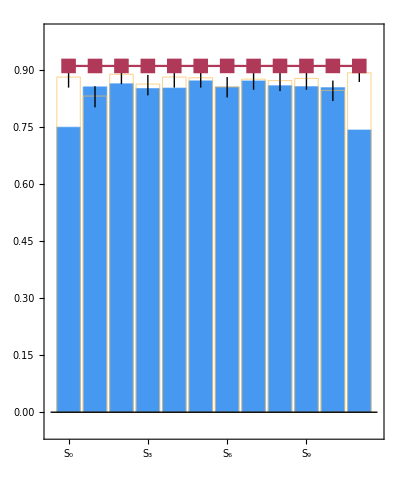
<|chart→-Graphics-,benchmark→{False,True,False,True,False,True,True,True,True,False,True,False}|>

Trial 2: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

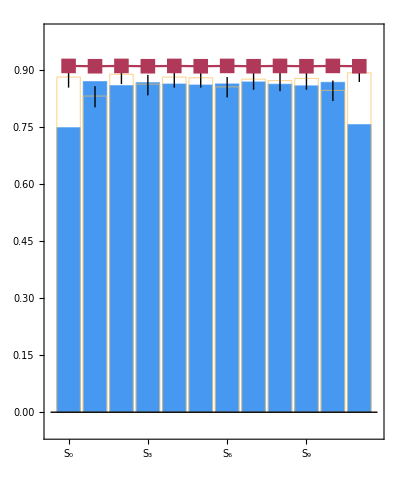
<|chart→-Graphics-,benchmark→{False,False,False,True,True,True,True,True,True,True,True,False}|>

Trial 3: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→100,FidMeas→0.975}

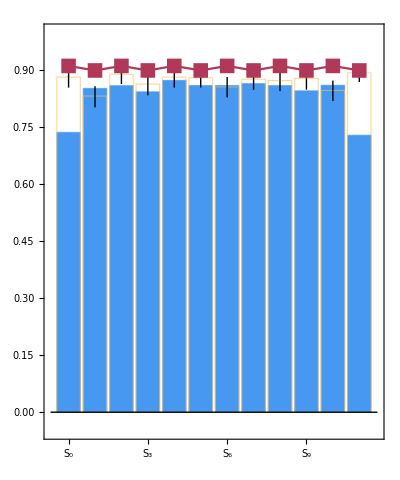
<|chart→-Graphics-,benchmark→{False,True,False,True,True,True,True,True,True,False,True,False}|>

Trial 4: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

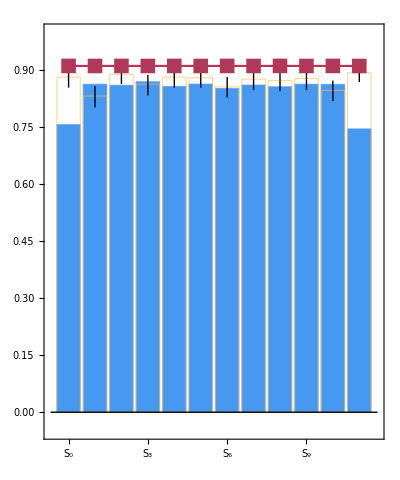
<|chart→-Graphics-,benchmark→{False,False,False,True,False,True,True,True,True,True,True,False}|>

Trial 5: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

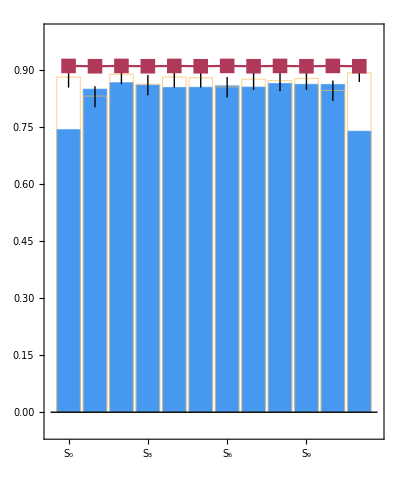
<|chart→-Graphics-,benchmark→{False,True,True,True,False,False,True,True,True,True,True,False}|>

Trial 6: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→100,FidMeas→0.975}

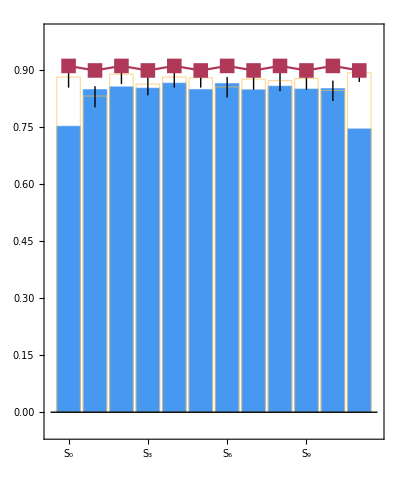
<|chart→-Graphics-,benchmark→{False,True,False,True,True,False,True,False,True,False,True,False}|>

```mathematica
graphstate1d<<graphstate1d.mx
```

graphstate1d Null

Trial 1: {}

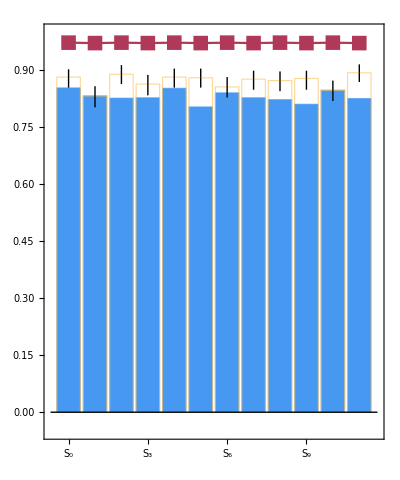
<|chart→-Graphics-,benchmark→{False,True,False,False,False,False,True,False,False,False,True,False}|>

Trial 2: {ProbBFRot→<|10→0.001,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

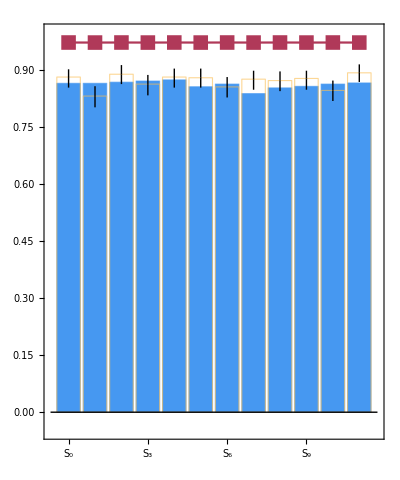
<|chart→-Graphics-,benchmark→{True,False,True,True,True,True,True,False,True,False,True,False}|>

Trial 3: {ProbBFRot→<|10→0.001,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

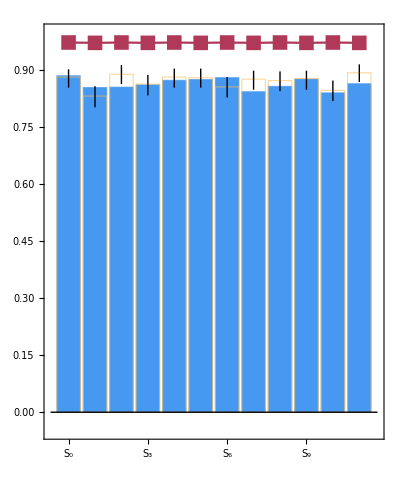
<|chart→-Graphics-,benchmark→{True,True,False,True,True,True,True,False,True,True,True,False}|>

Trial 4: {ProbBFRot→<|10→0.001,1→0.03|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

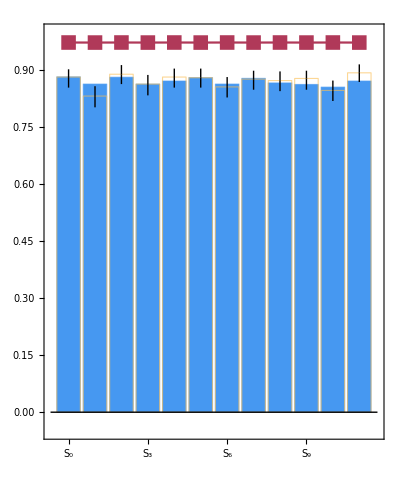
<|chart→-Graphics-,benchmark→{True,False,True,True,True,True,True,True,True,True,True,True}|>

Trial 5: {ProbBFRot→<|10→0.001,1→0.03|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

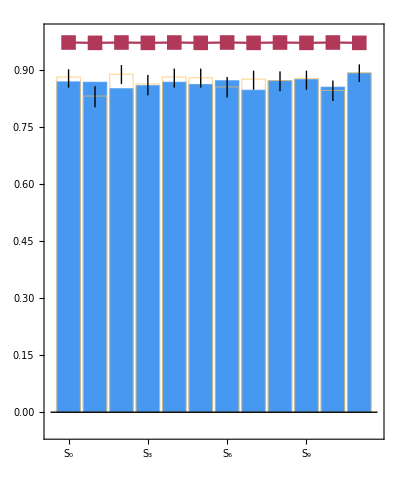
<|chart→-Graphics-,benchmark→{True,False,False,True,True,True,True,False,True,True,True,True}|>

Trial 6: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

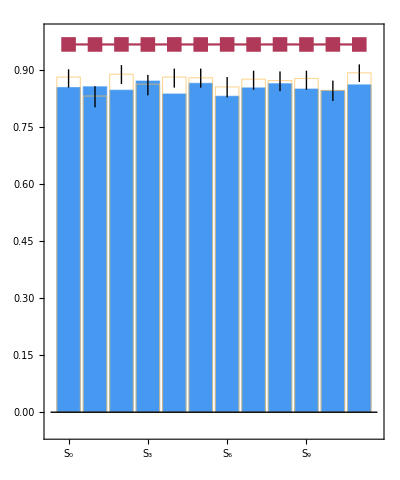
<|chart→-Graphics-,benchmark→{False,True,False,True,False,True,True,False,True,False,True,False}|>

Trial 7: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

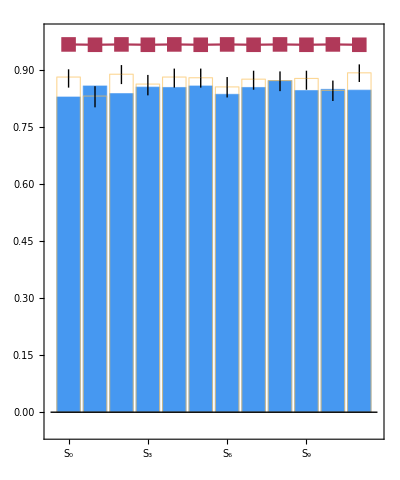
<|chart→-Graphics-,benchmark→{False,True,False,True,False,True,True,True,True,False,True,False}|>

Trial 8: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

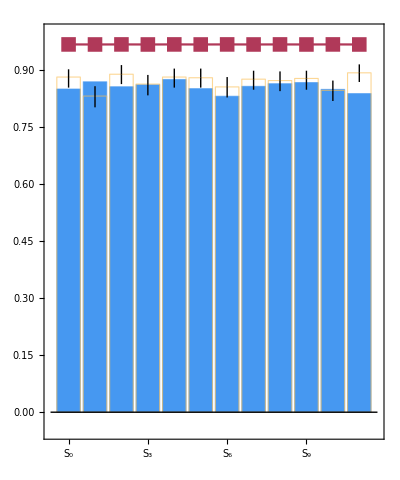
<|chart→-Graphics-,benchmark→{False,False,False,True,True,False,True,True,True,True,True,False}|>

Trial 9: {ProbBFRot→<|10→0.001,1→0.04|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

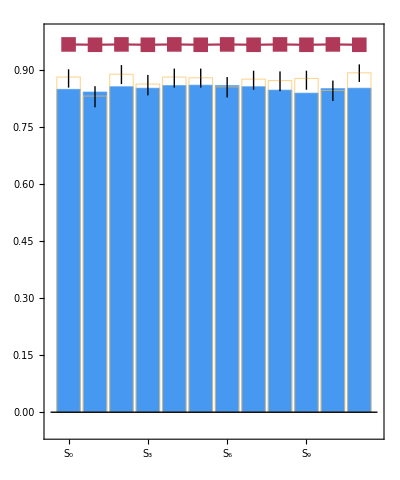
<|chart→-Graphics-,benchmark→{False,True,False,True,False,True,True,True,False,False,True,False}|>

Trial 10: {ProbBFRot→<|10→0.0001,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

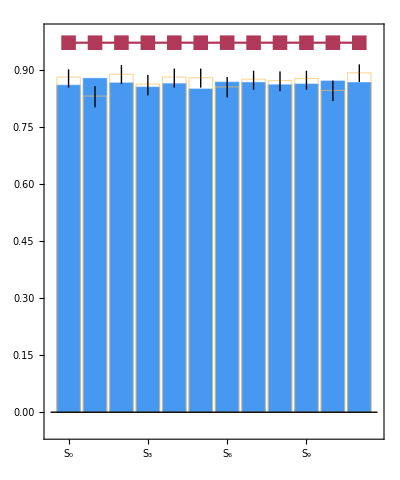
<|chart→-Graphics-,benchmark→{False,False,True,True,True,False,True,True,True,True,True,False}|>

Trial 11: {ProbBFRot→<|10→0.0001,1→0.03|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

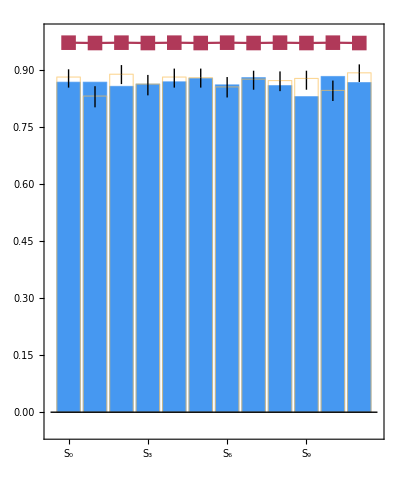
<|chart→-Graphics-,benchmark→{True,False,False,True,True,True,True,True,True,False,False,False}|>

Trial 12: {ProbBFRot→<|10→0.0001,1→0.03|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

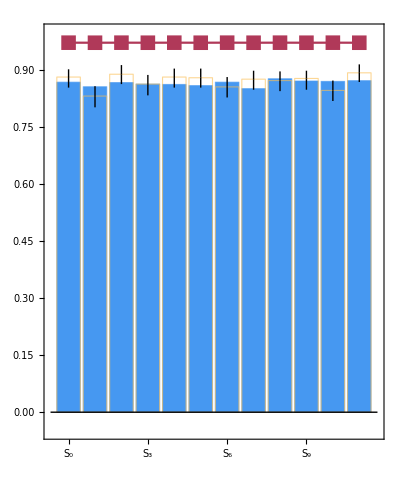
<|chart→-Graphics-,benchmark→{True,True,True,True,True,True,True,False,True,True,True,True}|>

Trial 13: {ProbBFRot→<|10→0.0001,1→0.03|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

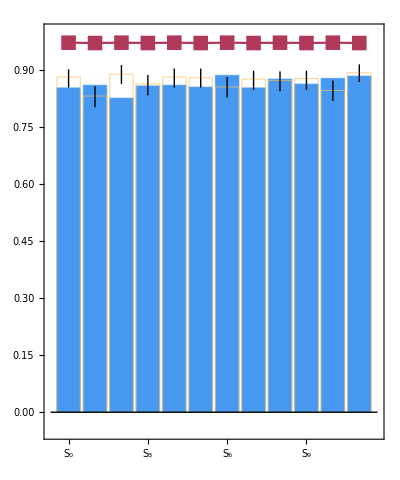
<|chart→-Graphics-,benchmark→{False,True,False,True,True,False,False,False,True,True,False,True}|>

Trial 14: {ProbBFRot→<|10→0.0001,1→0.04|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

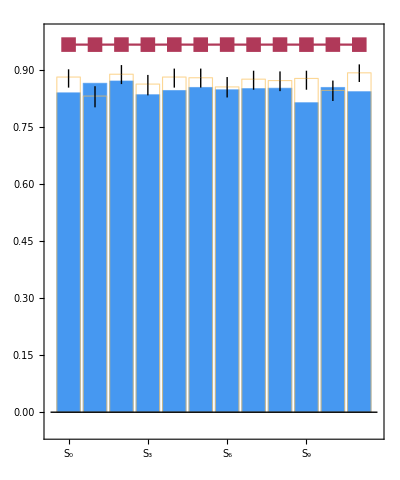
<|chart→-Graphics-,benchmark→{False,False,True,False,False,False,True,False,True,False,True,False}|>

Trial 15: {ProbBFRot→<|10→0.0001,1→0.04|>,ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

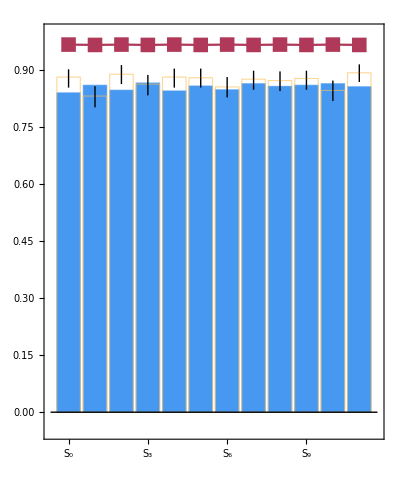
<|chart→-Graphics-,benchmark→{False,True,False,True,False,True,True,True,True,True,True,False}|>

Trial 16: {ProbBFRot→<|10→0.0001,1→0.04|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

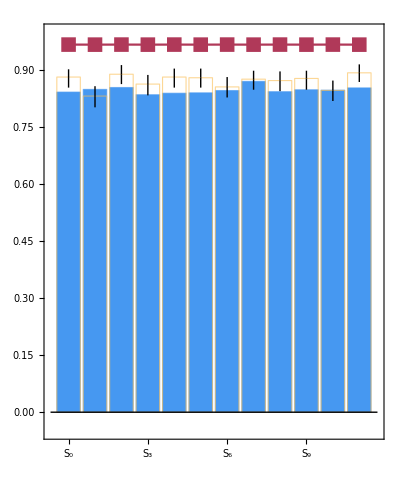
<|chart→-Graphics-,benchmark→{False,True,False,False,False,False,True,True,False,False,True,False}|>

Trial 17: {ProbBFRot→<|10→0.0001,1→0.04|>,ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

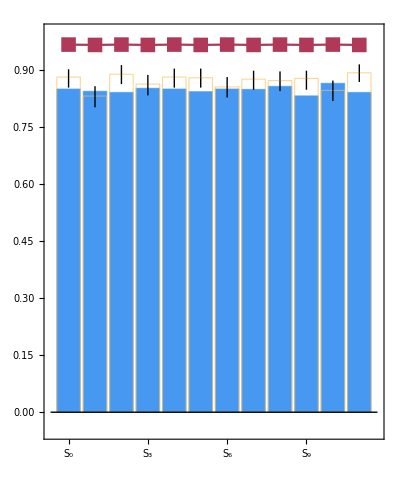
<|chart→-Graphics-,benchmark→{False,True,False,True,False,False,True,False,True,False,True,False}|>

```mathematica
(* another round, 2k shots *)
i=0;
Table[
Print["Trial ",++i,": ",opt];
out=SimulateGraphState[ρ,ρinit,ρwork,ρstore,2000,opt];
AppendTo[graphstate1d,out];
DumpSave["graphstate1d.mx",graphstate1d];
Print@showResults[out,cs1d][[{"chart","benchmark"}]];
,{opt,options}];
```

```mathematica
(* narrow down different shots *)
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.01,0.02}},{j,{0.0001}}];
heat={8,16,32,64};
fidmeas={0.975};
options=Flatten[Table[{ProbLeakCZ->k,HeatFactor->l,FidMeas->j},{k,probleakcz},{l,heat},{j,fidmeas}],2]
Length@options
```

{{ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975},{ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→16,FidMeas→0.975},{ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→32,FidMeas→0.975},{ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,FidMeas→0.975},{ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→8,FidMeas→0.975},{ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→16,FidMeas→0.975},{ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→32,FidMeas→0.975},{ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→64,FidMeas→0.975}}

8

```mathematica
nshots={1000,5000,10000};
```

nshots=1000

Trial 1: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

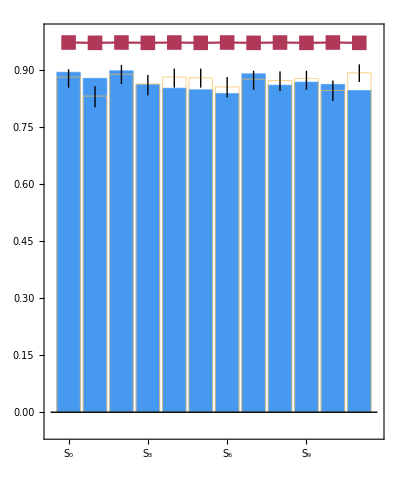
<|chart→-Graphics-,benchmark→{True,False,True,True,False,False,True,True,True,True,True,False}|>

Trial 2: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→16,FidMeas→0.975}

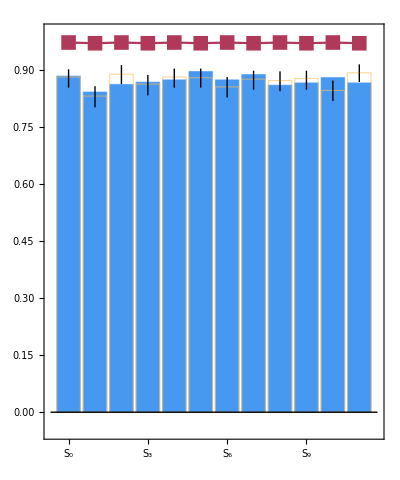
<|chart→-Graphics-,benchmark→{True,True,False,True,True,True,True,True,True,True,False,False}|>

Trial 3: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→32,FidMeas→0.975}

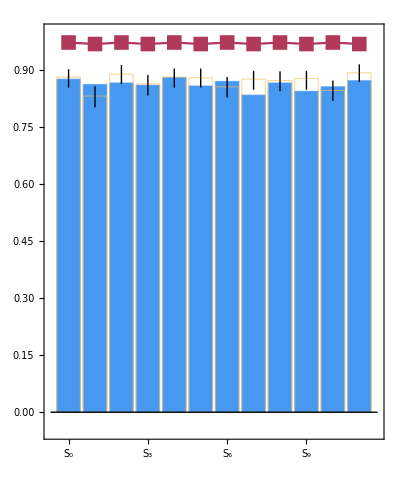
<|chart→-Graphics-,benchmark→{True,False,True,True,True,True,True,False,True,False,True,True}|>

Trial 4: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

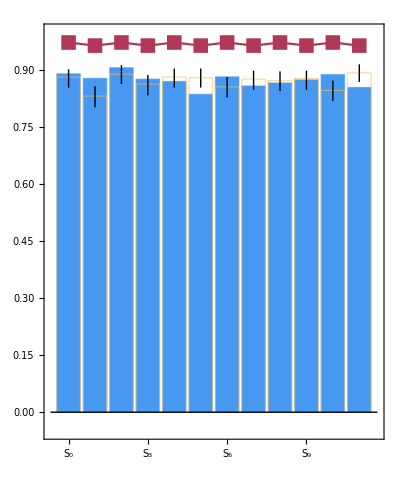
<|chart→-Graphics-,benchmark→{True,False,True,True,True,False,True,True,True,True,False,False}|>

Trial 5: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

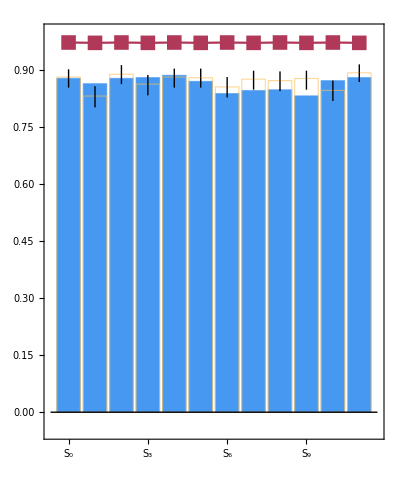
<|chart→-Graphics-,benchmark→{True,False,True,True,True,True,True,False,False,False,True,True}|>

Trial 6: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→16,FidMeas→0.975}

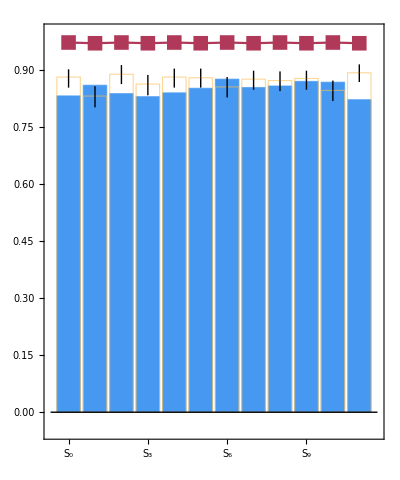
<|chart→-Graphics-,benchmark→{False,True,False,False,False,False,True,True,True,True,True,False}|>

Trial 7: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→32,FidMeas→0.975}

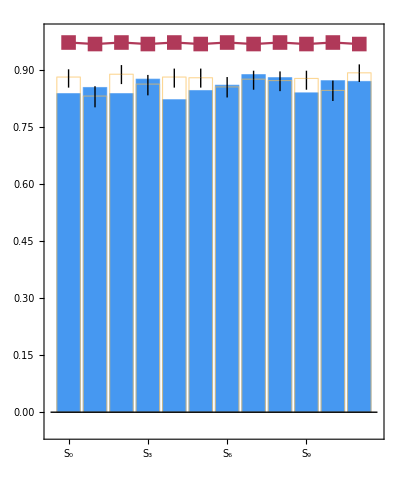
<|chart→-Graphics-,benchmark→{False,True,False,True,False,False,True,True,True,False,True,False}|>

Trial 8: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

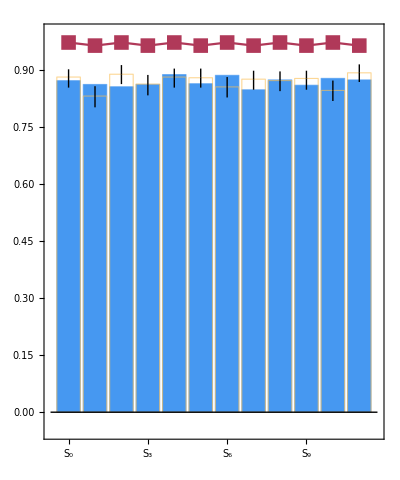
<|chart→-Graphics-,benchmark→{True,False,False,True,True,True,False,False,True,True,False,True}|>

nshots=5000

Trial 9: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

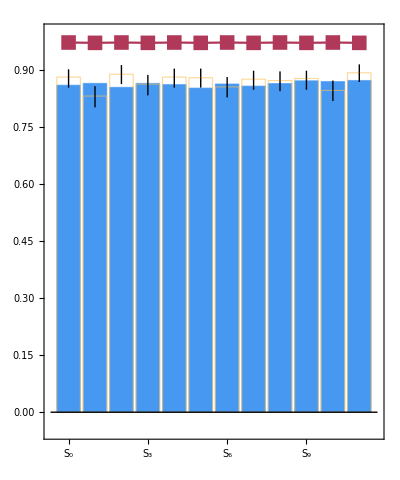
<|chart→-Graphics-,benchmark→{False,False,False,True,True,False,True,True,True,True,True,True}|>

Trial 10: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→16,FidMeas→0.975}

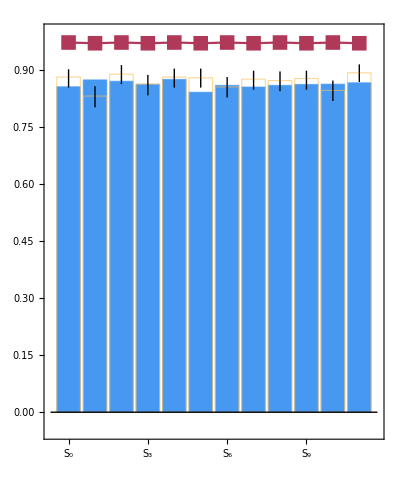
<|chart→-Graphics-,benchmark→{False,False,True,True,True,False,True,True,True,True,True,False}|>

Trial 11: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→32,FidMeas→0.975}

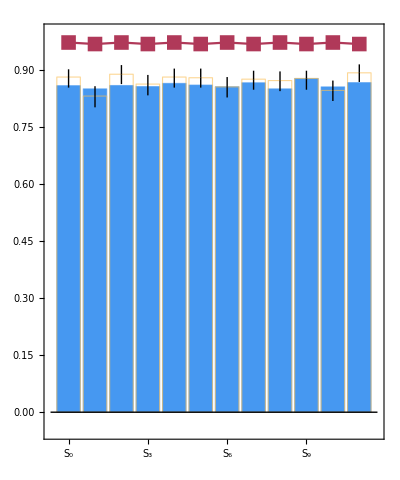
<|chart→-Graphics-,benchmark→{False,True,False,True,True,True,True,True,True,True,True,False}|>

Trial 12: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

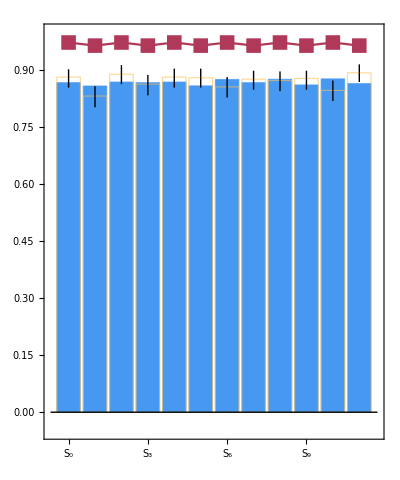
<|chart→-Graphics-,benchmark→{True,True,True,True,True,True,True,True,True,True,False,False}|>

Trial 13: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

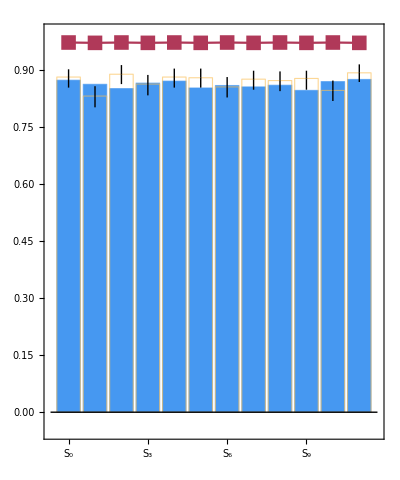
<|chart→-Graphics-,benchmark→{True,False,False,True,True,False,True,True,True,False,True,True}|>

Trial 14: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→16,FidMeas→0.975}

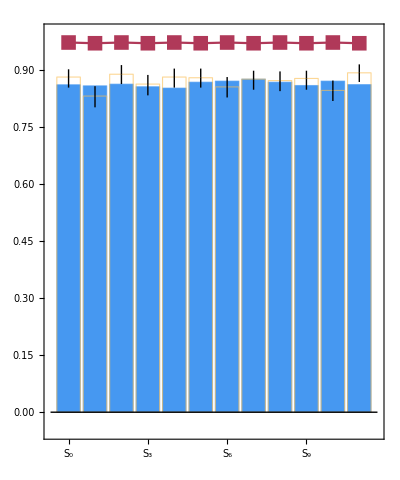
<|chart→-Graphics-,benchmark→{True,True,False,True,False,True,True,True,True,True,True,False}|>

Trial 15: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→32,FidMeas→0.975}

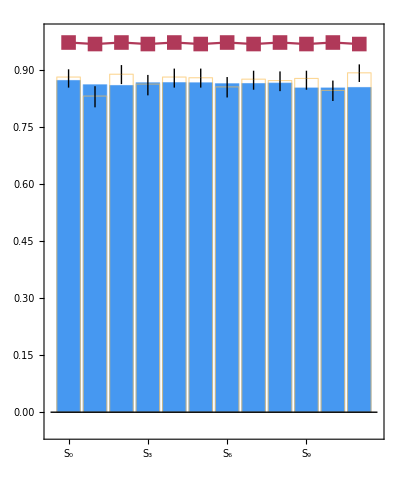
<|chart→-Graphics-,benchmark→{True,False,False,True,True,True,True,True,True,False,True,False}|>

Trial 16: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

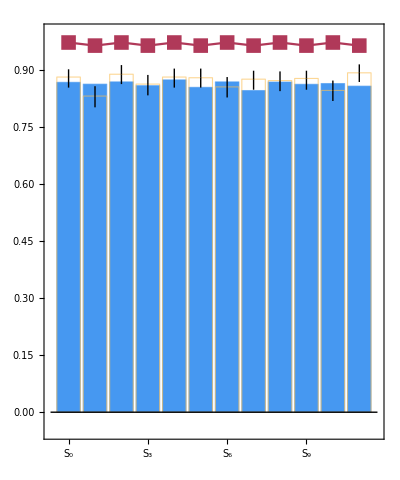
<|chart→-Graphics-,benchmark→{True,False,True,True,True,False,True,False,True,True,True,False}|>

nshots=10000

Trial 17: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

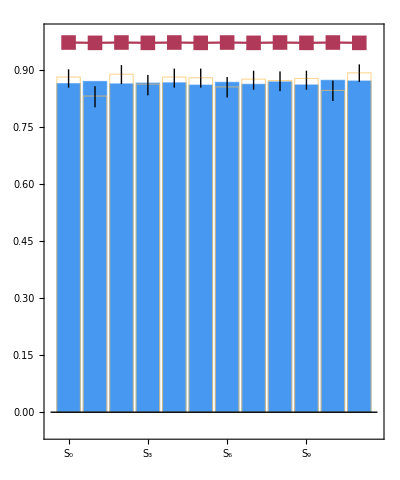
<|chart→-Graphics-,benchmark→{True,False,False,True,True,True,True,True,True,True,True,True}|>

Trial 18: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→16,FidMeas→0.975}

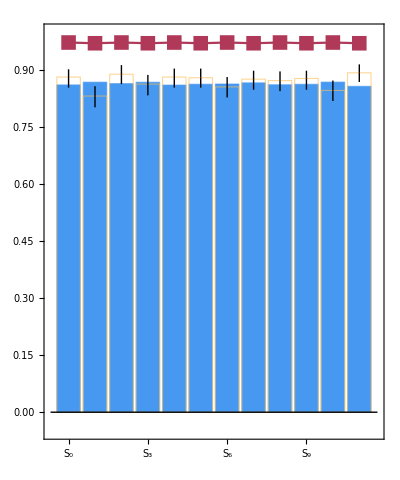
<|chart→-Graphics-,benchmark→{False,False,False,True,True,True,True,True,True,True,True,False}|>

Trial 19: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→32,FidMeas→0.975}

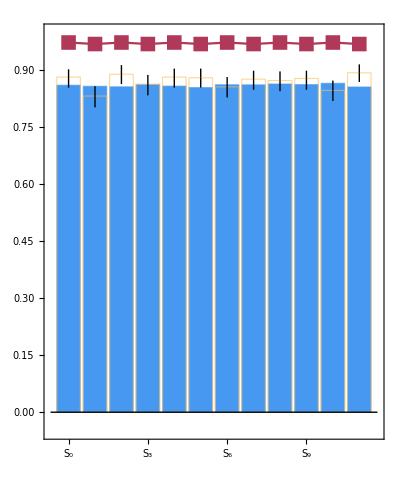
<|chart→-Graphics-,benchmark→{False,True,False,True,False,False,True,True,True,True,True,False}|>

Trial 20: {ProbLeakCZ→<|10→0.01,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

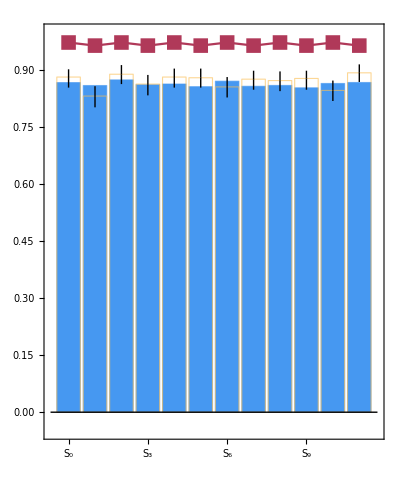
<|chart→-Graphics-,benchmark→{True,True,True,True,True,True,True,True,True,False,True,False}|>

Trial 21: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

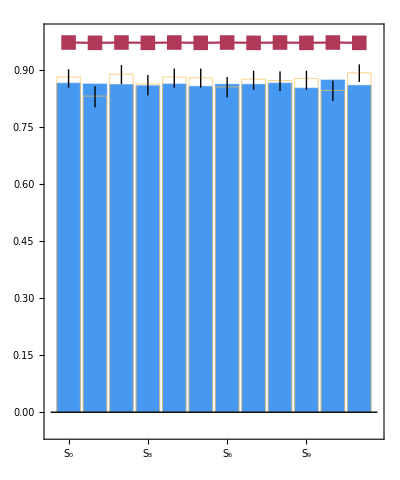
<|chart→-Graphics-,benchmark→{True,False,False,True,True,True,True,True,True,False,True,False}|>

Trial 22: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→16,FidMeas→0.975}

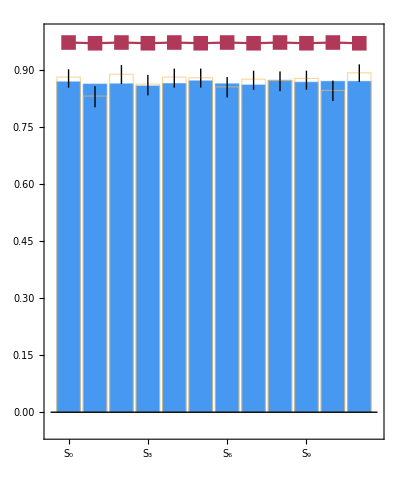
<|chart→-Graphics-,benchmark→{True,False,False,True,True,True,True,True,True,True,True,False}|>

Trial 23: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→32,FidMeas→0.975}

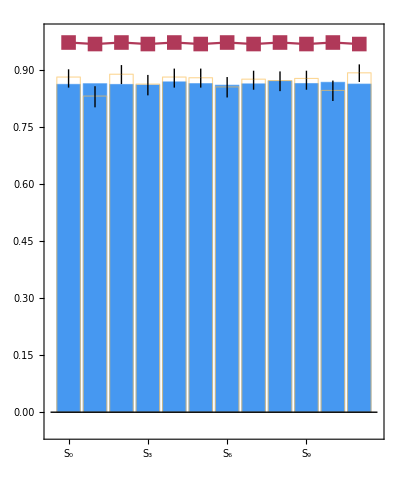
<|chart→-Graphics-,benchmark→{True,False,False,True,True,True,True,True,True,True,True,False}|>

Trial 24: {ProbLeakCZ→<|10→0.02,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

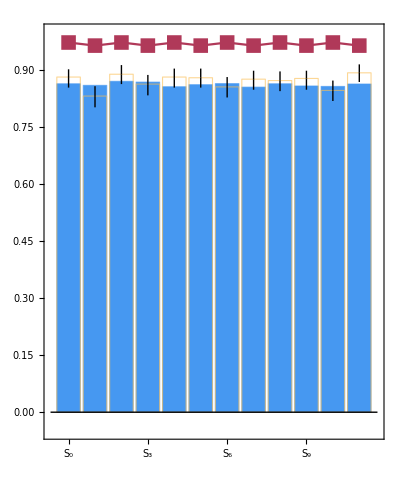
<|chart→-Graphics-,benchmark→{True,True,True,True,False,True,True,True,True,True,True,False}|>

```mathematica
i=0;
Table[
Print["nshots=",shot];
Table[
Print["Trial ",++i,": ",opt];
out=SimulateGraphState[ρ,ρinit,ρwork,ρstore,shot,opt];
AppendTo[graphstate1d,out];
DumpSave["graphstate1d.mx",graphstate1d];
Print@showResults[out,cs1d][[{"chart","benchmark"}]];
,{opt,options}]
,{shot,nshots}];
```